## Perturbation Sensitivity Plots of Potential Example Rules

```mathematica
ars = [[All, 1]];
```

```mathematica
trs = ;
```

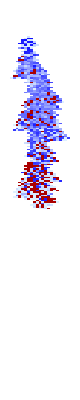
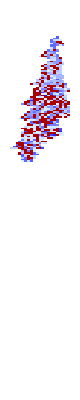
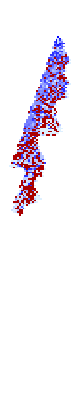
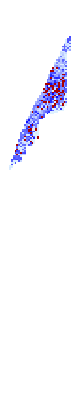
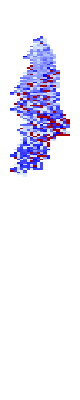
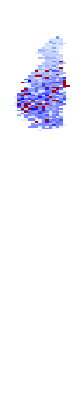
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[;;10]]]
```

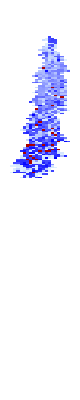
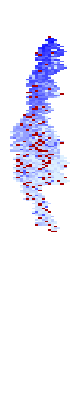
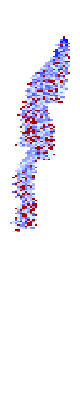
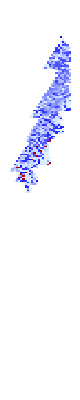
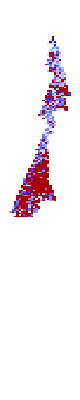
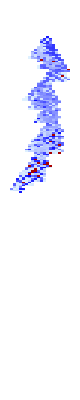
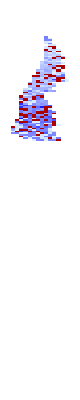
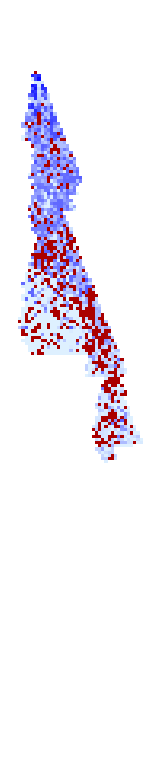

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[11;;20]]]
```

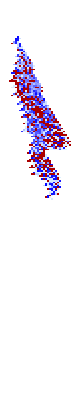
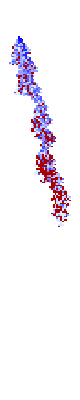
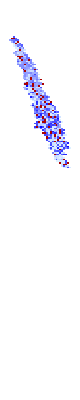
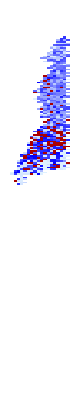
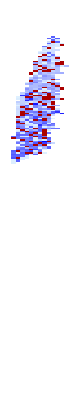
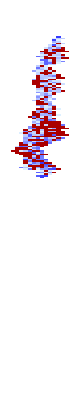
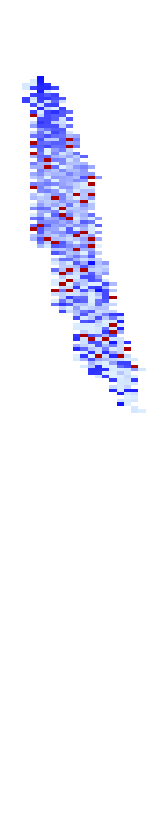
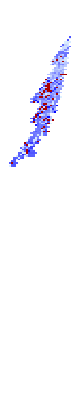
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[21;;30]]]
```

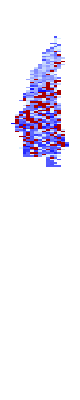
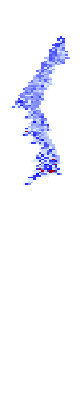
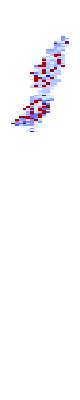
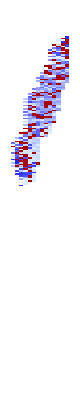
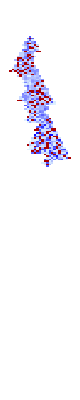
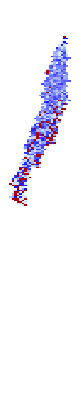
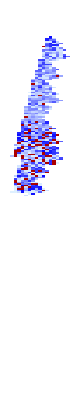
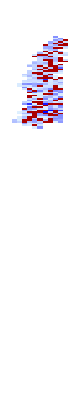
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[31;;40]]]
```

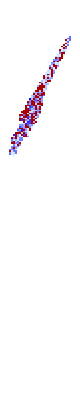
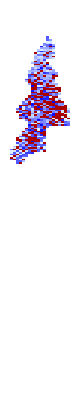
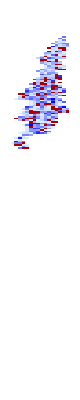
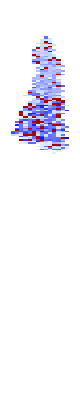
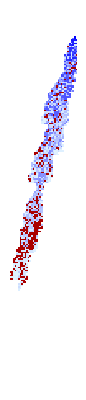
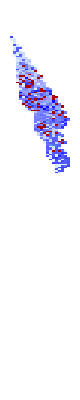
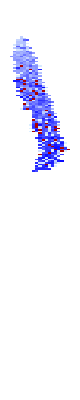
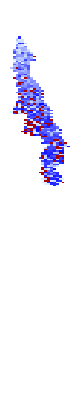
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[41;;52]]]
```

```mathematica
plotrule[trs[[49]]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[trs[[49]], "ReturnPerturbations"->True], 10]]
```

-Graphics-

```mathematica
trs2[[98]]
```

{201412842028162214137229450141139961424,4,1}

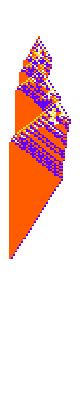

```mathematica
PlotCA[trs2[[98]]]
```

```mathematica
trs2 = ;
```

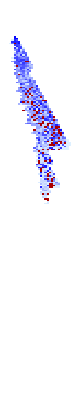
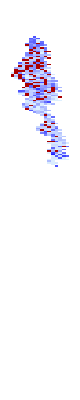
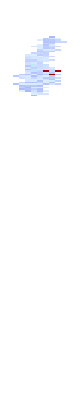
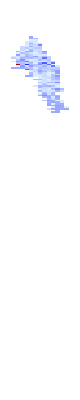
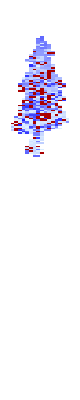
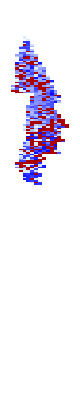
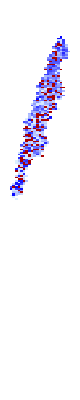
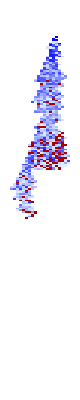

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[;;10]]]
```

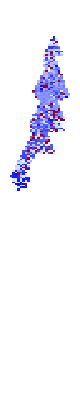
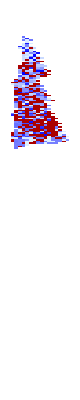
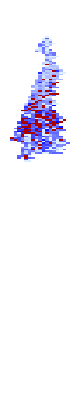
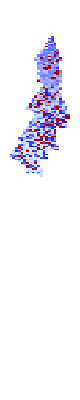
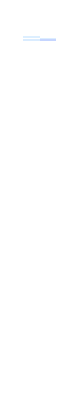
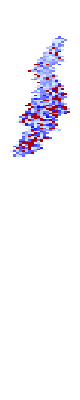
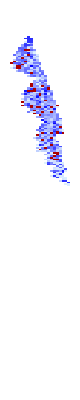
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[11;;20]]]
```

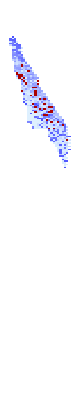
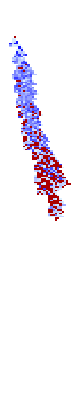
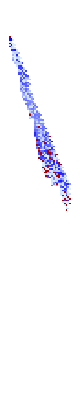
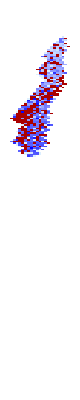
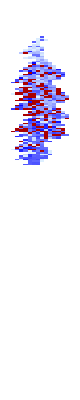
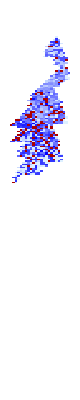
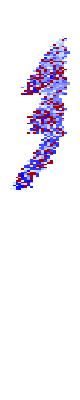
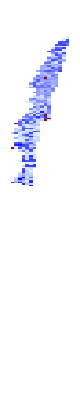
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[21;;30]]]
```

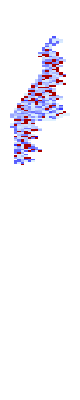
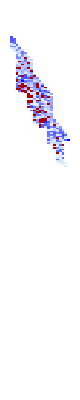
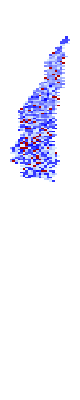
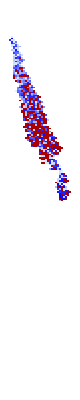
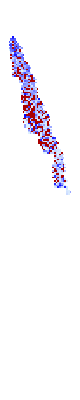
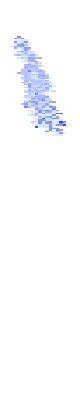
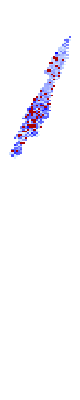
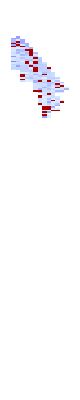
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[31;;40]]]
```

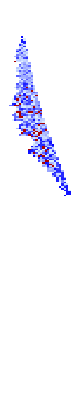
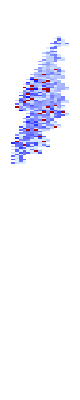
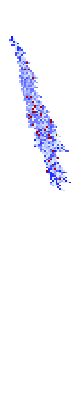
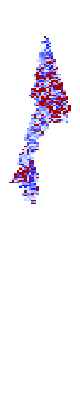
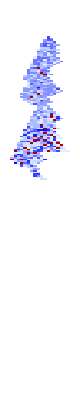
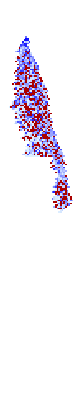
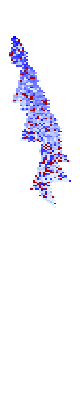
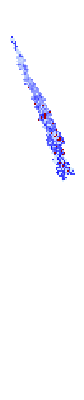
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[41;;60]]]
```

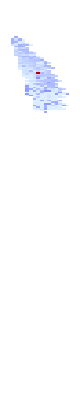
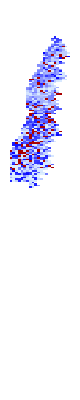
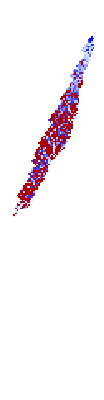
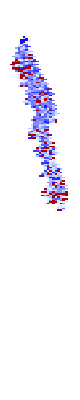
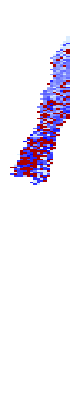
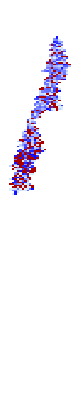
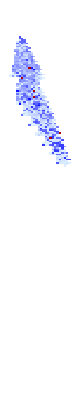
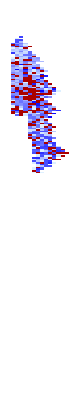
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[61;;70]]]
```

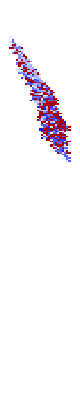
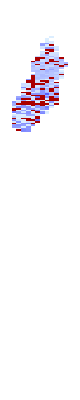
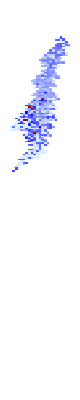
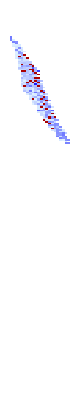
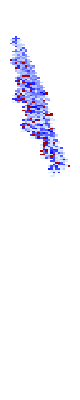
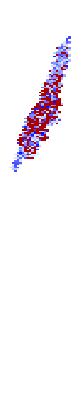
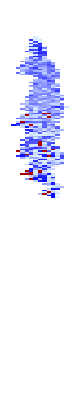
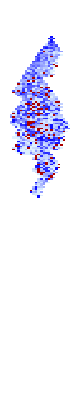
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[71;;80]]]
```

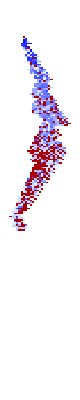
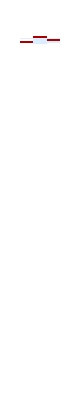
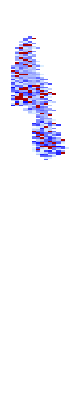
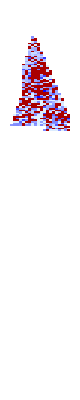
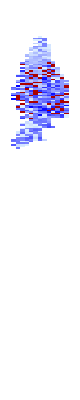
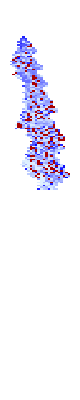
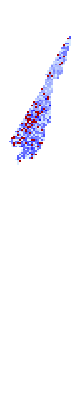
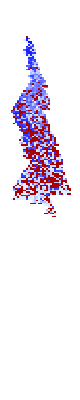

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[81;;90]]]
```

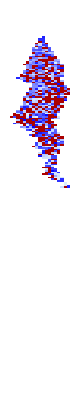
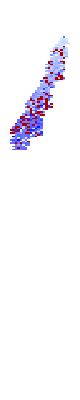
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[91;;100]]]
```

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[101;;110]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[111;;120]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[121;;130]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[131;;140]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[141;;148]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[trs2]
```

148

```mathematica
PlotCA[getca[trs2[[58]]]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[trs[[12]],NRandomPerts[1, getca[trs[[12]]]], "ReturnPerturbations"->True], 10]]
```

-Graphics-

## Evolving With Same Perturbations Every Time

```mathematica
SeedRandom[333999];
perts = Transpose@{RandomInteger[{1, 100}, 20], RandomInteger[{40, 60}, 20]};
evosame = AdaptCA[{0, 4, 1}, 1000, "AutomatonFunction"->(getca[#, 200, 100, CenterArray[1, 100]]&), "Perturbation"->perts, "ReturnCAs"->True, "ReturnPerturbations"->True, "BitFunc"->("SetValue"->0)];
```

```mathematica
GraphicsRow[PlotCA[#[[1, "cas", 2]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evosame
```

-Graphics-

```mathematica
With[{ca =getca[evosame[[-1, "rule"]], 200, 100, CenterArray[1, 100]]}, Table[PlotCA[PerturbCA[{ca, evosame[[-1, "rule"]]}, "Random"->{1, "Random", "SetValue"->0}]], 10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ca =getca[evosame[[-1, "rule"]], 200, 100, CenterArray[1, 100]]},PerturbationSensitivityPlot[{ca,  evosame[[-1, "rule"]]}, absdeltalt(*, "SetValue"->0*)]]
```

-Graphics-

## Evolving Genetic Robustness

```mathematica
geneticpertfunc[{ca_, ru_}]:= getca[RandomRuleMutation[ru], Length[ca]]
```

```mathematica
SeedRandom[4603];
evo4 = AdaptCA[{0, 4, 1}, 2000,"PerturbationFunction"->geneticpertfunc, "NPerturbations"->3];
evo4[[-1, "fitness"]]
GraphicsRow[PlotCA[#[[1,"rule"]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo4
```

71

-Graphics-

```mathematica
plotmaskedrule[evo4[[-1, "rule"]], ImageSize->1000]
```

-Graphics-

```mathematica
Table[PlotCA[RandomRuleMutation[evo4[[-1, "rule"]]]], 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Takeaway: Genetic robustness is much harder than robustness to perturbations. Why? Unclear

```mathematica
Histogram[Table[TestLifetime[{{"[◼]", "RandomRuleMutation"}}[ evo4[[-1, "rule"]]], 200], 1000]/.-Infinity->0]
```

-Graphics-

### Regular for comparison

```mathematica
SeedRandom[333775];
evo3 = AdaptCA[{0, 4, 1}, 1000, "ReturnCAs"->True, "ReturnPerturbations"->True];
```

```mathematica
GraphicsRow[PlotCA[#[[1,"rule"]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo3
```

-Graphics-

```mathematica
plotmaskedrule[GatherBy[evo3, #fitness&][[8, 1, "rule"]]]
```

-Graphics-

```mathematica
PlotCA[GatherBy[evo3, #fitness&][[8, 1, "rule"]]]
```

-Graphics-

```mathematica
Histogram[Table[TestLifetime[{{"[◼]", "RandomRuleMutation"}}[GatherBy[evo3, #fitness&][[5, 1, "rule"]]], 200], 1000]/.-Infinity->0]
```

-Graphics-

### k = 5

```mathematica
geneticpertfunc[{ca_, ru_}]:= getca[RandomRuleMutation[ru], Length[ca]]
```

```mathematica
SeedRandom[4600];
evo = AdaptCA[{0, 5, 1}, 2000,"PerturbationFunction"->geneticpertfunc, "NPerturbations"->5];
evo[[-1, "fitness"]]
GraphicsRow[PlotCA[#[[1,"rule"]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo
```

37

-Graphics-

```mathematica
plotrule[evo[[-1, "rule"]]]
```

-Graphics-

```mathematica
evo[[-1, "rule"]]
```

{63603350490056248387374234882853345539893717923014906631901432550947254713231151216225,5,1}

```mathematica
plotmaskedrule[evo[[-1, "rule"]], ImageSize->1000]
```

-Graphics-

```mathematica
Table[PlotCA[RandomRuleMutation[evo[[-1, "rule"]]]], 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Takeaway: Genetic robustness is much harder than robustness to perturbations. Why? Unclear

```mathematica
Histogram[Table[TestLifetime[{{"[◼]", "RandomRuleMutation"}}[ evo[[-1, "rule"]]], 200], 1000]/.-Infinity->0]
```

-Graphics-

## Genetic Diseases for Lower Frequency Rules on Somewhat Genetically Robust Rule

```mathematica
Module[{ru ={111090216534690761884340967837163343472,4,1}, ca}, ca = getca[ru];
Echo@PlotCA[ca, "Trim"->{1, 1}];
RuleFrequencyChart[{ca, ru}, "ShowSequences"->True,"TuplesFunction"->(2#+1&)]]
```

-Graphics-

-Graphics-

```mathematica
mutaterule[{n_Integer, k_Integer, r_Integer}, sequence_ ,bitfunc_:"Random"]:= Module[{
tups = Reverse[Tuples[Range[0, k - 1], 1 + 2r]], 
digs = IntegerDigits[n, k, k^(2r+1)], pos},
pos =  First[FirstPosition[tups, sequence]];
{FromDigits[ReplacePart[digs, pos->todirectfunc[bitfunc, k][digs[[pos]]]], k],k, r}]
```

```mathematica
Module[{ru ={111090216534690761884340967837163343472,4,1}, ca, counts}, ca = getca[ru];
counts = ReverseSort[Counts[Flatten[activebodytups[{ca, ru}, (2#+1&)], 1]]];
Table[PlotCA[mutaterule[ru, Keys[counts][[i]]]], {i, 64}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Kicking the TV

```mathematica
PlotCA[trs2[[98]]]
```

-Graphics-

```mathematica
cps = getcancerperts[trs2[[98]]];
```

```mathematica
Length[cps]
```

225

```mathematica
PlotCA[PerturbCA[trs2[[98]],#, 500]]&/@ cps[[;;50]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Multiway Graph

## Drugs

## Clinical Trials on Other Rules

## New AdaptCA function for larger search

With support for perturbation specifications

```mathematica
SeedRandom[333768];
evo = AdaptCA[{0, 4, 1}, 500,   "ReturnCAs"->True, "Perturbation"->True, "NPerturbations"->2, "ReturnPerturbations"->True];
```

And support for drawing arrows

```mathematica
GraphicsGrid[Partition[GraphicsRow[#]& /@(PlotCA[#(*, "Trim"->{1, 10}*)]&/@#[[1, "cas"]]&/@ GatherBy[evo, #fitness&]), 5], ImageSize->1000]
```

-Graphics-

### TODO: Magnification

## Running more evolutions

```mathematica
evos = ParallelTable[SeedRandom[4468+ i];
 AdaptCA[{0, 4, 1}, 1000, "Perturbation"->("NRandom"->3),"NPerturbations"->5], {i, 3}];
```

```mathematica
GraphicsRow[PlotCA[#[[1, "rule"]]]&/@ GatherBy[#, #fitness&]]&/@ evos
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[evos[[2, -1, "rule"]],"NRandom"->1], 10]]
```

-Graphics-

## Init

```mathematica
k4rob =Select[ , Last[#]>100&];
k4reg= Select[,Last[#]>100&];
```

```mathematica
psrob = ;
```

```mathematica
msrob = N[Mean/@ psrob];
```

```mathematica
psreg = ;
```

```mathematica
msreg = N[Mean/@ psreg];
```

```mathematica
sirob = SortBy[Range[Length[k4rob]], msrob[[#]]&];
```

```mathematica
sireg = SortBy[Range[Length[k4reg]], msreg[[#]]&];
```

```mathematica
ru = k4rob[[sirob[[15]],1]];
{n, k, r} = ru;
pat = getca[ru, 200];
ca = pat;
lt = TestCALifeTime[ca];
```

```mathematica
cps2 = getcancerperts[ru];
```

```mathematica
cps2[[10]]
```

9→{{4},Enumerate,AddValue→1}

```mathematica
hs = gethealers[ru, cps2[[10]](*, (# <= 180&)*)];
```

```mathematica
PlotCA[PerturbCA[ru, cps2[[10]]]]
```

-Graphics-

```mathematica
PlotCA[PerturbCA[{ca, ru}, 30->3]]
```

-Graphics-

## Code for larger search

### Getting promising biological matter

```mathematica
{297413941736399379873447198801621939512,4,1}
```

```mathematica
{22319669923744036423938755597589056072,4,1}
```

```mathematica
regrus = [[All, 1]];
```

```mathematica
promisingseeds = (Position[, {_, n_Integer}/;n >= 10][[All, 1]]) + 426778;
```

```mathematica
goodseed = 667893;
```

```mathematica
goodseed = 667914;
```

```mathematica
(*Module[{perts = Transpose@{RandomInteger[{30, 50}, 20], RandomInteger[{40, 60}, 20]}},
Echo[perts];*)
ClearAll@pertfunc
pertfunc[{ca_, ru_}]:=  Module[{left, right, bottom, perts}, 
perts = Transpose@{RandomInteger[{60, 80}, 20], RandomInteger[{40, 60}, 20]};
{{left, right}, bottom} = gettrimoffsets[ca, {0, 0}];
inbody = Select[perts, With[{range = nonzeroRange[ca[[#[[1]]]]]}, 
range!={}&&#[[1]]<= TestCALifeTime[ca]&&#[[2]]>= range[[1]]&& #[[2]]<= range[[2]]]&];
If[inbody === {}, ca,
PerturbCA[{ca, ru},inbody]]]
(*]*)
```

### Running Evolution

```mathematica
ClearAll@pf2
```

```mathematica
pf2[{ca_, ru_}]:= PerturbCA[{ca, ru}, RandomInteger[{30, 60}]->1]
```

```mathematica
SeedRandom[promisingseeds[[2]]];
evo = AdaptCA[{0, 4, 1}, 3000, "PerturbationFunction"->pf2, "NPerturbations"->5, "ReturnCAs"->True, "ReturnPerturbations"->True, "CombinationFunction"->Min(*(#[[1]] - Mean[Abs[#[[1]] - Rest[#]]]&)*)];
```

```mathematica
GraphicsRow[PlotCA[#[[1,"rule"]]]&/@ GatherBy[#, #fitness&]]&/@{evo}
```

{-Graphics-}

```mathematica
PerturbationSensitivityPlot[{getca[evo[[-1, "rule"]]], evo[[-1, "rule"]]}]
```

-Graphics-

```mathematica
ListLinePlot[evo[[All, "fitness"]], PlotRange->All]
```

-Graphics-

### Code to run for AWS

```mathematica
promisingevoobjects = Select[ParallelTable[AdaptCA[{0, 4, 1}, 300][[-1]], 2], #fitness >= 10&];
```

```mathematica
ParallelMap[AdaptCA[Append[#, "cas"->{}],500, "PerturbationFunction"-> (PerturbCA[#, RandomInteger[{10, 40}]->1]&), "NPerturbations"->5]&, promisingevoobjects]
```

```mathematica
evos = Module[{},
Echo["Finding promising rules"];
promisingevoobjects= Append[#, "cas"->{}]&/@Select[ParallelTable[AdaptCA[{0, 4, 1}, 300][[-1]], 10], #fitness >= 10&];
Echo["Running robust evolutions"];
ParallelMap[AdaptCA[#,500, "PerturbationFunction"-> (PerturbCA[#, RandomInteger[{10, 40}]->1]&), "NPerturbations"->5]&, promisingevoobjects]
];
```

Finding promising rules

Running robust evolutions

```mathematica
promisingevoobjects
```

{}

```mathematica
GraphicsRow[PlotCA[#[[1,"rule"]]]&/@ GatherBy[#, #fitness&]]&/@evos
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbationSensitivityPlot[{getca[evos[[5, -1, "rule"]]], evos[[2, -1, "rule"]]}]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[{getca[promisingevoobjects[[1, "rule"]]], promisingevoobjects[[1, "rule"]]}]
```

-Graphics-

```mathematica
es = AdaptCAFinal[<|"rule"->{297413941736400589979939780692294751544,4,1}, "fitness"->12|>];
```

```mathematica
es[[1]]
```

<|rule→{297413941736400589979939780692294751544,4,1},fitness→12|>

```mathematica
<|"rule"->{297413941736400589979939780692294751544,4,1},"fitness"->12|>
```

```mathematica
obj = AdaptCAWhile[{0,4,1}, (#fitness<20&), 500]
```

<|rule→{99721785856736681901915310172097647244,4,1},fitness→27|>

```mathematica
ru = AdaptCAFinal[obj,1000, "PerturbationFunction"->PerturbCA, "NPerturbations"->5 ]["rule"]
```

{99721785856736678360140448019897170572,4,1}

```mathematica
PlotCA[ru]
```

-Graphics-

```mathematica
PerturbationSensitivityPlot[{getca[ru], ru}]
```

-Graphics-

```mathematica
Length[trs] + 98
```

150

### Trying to replicate big red

```mathematica
PerturbCAFast[{getca[ars[[150]]], ars[[150]]}, "Random"->1]
```

```mathematica
randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
```

```mathematica
SeedRandom[426778+150];
e9 = NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->1], Ceiling[lt/20]];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000];
```

```mathematica
e9[[-1]]
```

{{269782796655236205240422954270170072844,4,1},7}

```mathematica
PlotCA[e9[[-1, 1]]]
```

-Graphics-

```mathematica
evo3 = Module[{ru, ca, lt, pcas,lts,  fitness},
SeedRandom[426778+132];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
{pcas, perts} = Transpose[Table[PerturbCA[{ca, ru}, RandomInteger[{1, lt}]->1, "ReturnPerturbations"->True], 5]];
fitness = Min[lts = Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Min[Last[#]],{ru,perts, Join[{ca}, pcas], lts},#]
]]&,{{0,4,1},{}, {getca[{0, 4, 1}, 200]}, {0}},2000]
];
```